# DENEB v1.0.0

## TO DO DATA ANALYSIS WITH GRACE AND PLEASURE

## 一维：均值与不确定度

### 样本数据处理

#### 数据输入

```mathematica
SetDirectory["/Users/royalty/Documents/GitHub/Data-Analysis-Plantform-for-University-Physics-Basic-Experiment"]
(*设置工作路径到工作文件夹*)
```

/Users/royalty/Documents/GitHub/Data-Analysis-Plantform-for-University-Physics-Basic-Experiment

```mathematica
Clear["Global`*"]
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)

data1=Import["sampledata1.txt","List"]   (*从文件中读取数据，注意文件中数据的摆放形式：同组数据以空格间断、以回车符为一组数据的分割*)

(*或者也可以手动输入数据：data={1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02},不过有点麻烦*)

(*Export[]的使用方法和Import[]差不多，参见帮助文档*)
```

{1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02}

#### 不确定度计算

样本平均值:1.10889

样本标准差:0.0648931

A类不确定度:0.0499677

B类不确定度:0.0461976

展伸不确定度（P=0.95）:0.0680514

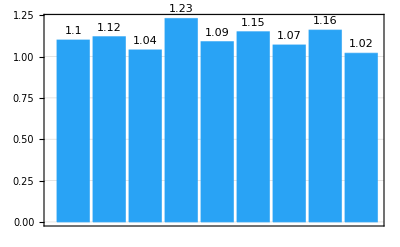

```mathematica
number=Length[data1];(*数组长度*)
average=Mean[data1]//N;(*平均值*)
st=StandardDeviation[data1]//N;(*data的标准差*)

(*A类不确定度*)
If[
number>21,
UA=Tdistribution[[22]]*st/Sqrt[number],
UA=Tdistribution[[number]]*st/Sqrt[number];
]

(*B类不确定度*)
gudu=0.05;        (*估读误差*)
yiqi=0.05;       (*仪器误差*)
zhixin=3;         (*置信系数*)
UB=1.96*(√(gudu^2+yiqi^2))/zhixin;

(*总不确定度*)
U=√(UA^2+UB^2);

(*输出*)
Print["样本平均值:",average]
Print["样本标准差:",st]
Print["A类不确定度:",UA]
Print["B类不确定度:",UB]
Print["展伸不确定度（P=0.95）:",U]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->RGBColor[0.16, 0.64, 0.96]
]
```

```mathematica
RandomColor[]
```

RGBColor[0.09798006958105376, 0.4145480748221486, 0.05306167632890646]

### 剔除异常

{1.1,1.12,1.04,1.23,1.09,1.15,1.07,1.16,1.02}

第 4 组数据 1.23 和平均值有最大相对偏差 10.9218%

剔除后平均值:1.09375

剔除后标准差:0.0495516. 相对之前变化：-0.0153415

剔除后A类不确定度:0.0381547. 相对之前变化：-0.011813

剔除后B类不确定度:0.0461976

剔除后展伸不确定度（P=0.95）:0.0599166. 相对之前变化：-0.00813474

-Graphics-

{1.1,1.12,1.04,1.09,1.15,1.07,1.16,1.02}

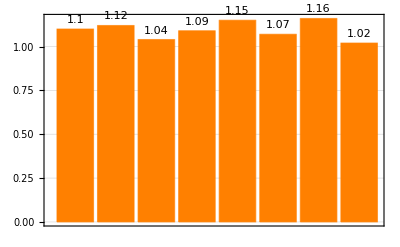

```mathematica
difference=Abs[data1-average];
data1
For[i=1,i<=number, i++,
If[difference[[i]]==Max[difference],
Print["第 ",i," 组数据 ",data1[[i]]," 和平均值有最大相对偏差 ",Max[difference]/average*100,"%"];
aim=i;
Break;
]]     (*for循环，寻找离平均值最远的点*)

t=0;
If[aim==1,newdata1=data1[[2;;number]];t=1;]
If[aim==number,newdata1=data1[[1;;number-1]];t=1;]
If[t!=1,forward=data1[[1;;aim-1]];back=data1[[aim+1;;number]];newdata1=Join[forward,back];]    (*剔除编号为aim的数据*)

newnumber=Length[newdata1];(*平均值*)
average=Mean[newdata1]//N;
newst=StandardDeviation[newdata1]//N;(*newdata的标准差*)
If[
newnumber>21,
newUA=Tdistribution[[22]]*newst/Sqrt[number],
newUA=Tdistribution[[number]]*newst/Sqrt[number];
](*A类不确定度*)

gudu=0.05;       (*估读误差*)
yiqi=0.05;      (*仪器误差*)
zhixin=3; (*置信系数*)
UB=1.96*(√(gudu^2+yiqi^2))/zhixin;(*B类不确定度*)

newU=√(newUA^2+UB^2);(*总不确定度*)

Print["剔除后平均值:",average]
Print["剔除后标准差:",newst,". 相对之前变化：",newst-st]
Print["剔除后A类不确定度:",newUA,". 相对之前变化：",newUA-UA]
Print["剔除后B类不确定度:",UB]
Print["剔除后展伸不确定度（P=0.95）:",newU, ". 相对之前变化：",newU-U]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->RGBColor[0.16, 0.64, 0.96]]

t=0;
t=Input["是否从测量序列中剔除此数（样本容量需要足够大）？确认请填1："];
If[t==1,data1=newdata1;number=newnumber;data1,data1]
BarChart[data1,PlotRange->Full,PlotTheme->"Detailed",ChartLabels->Placed[data1,Above],
ChartStyle->Orange]
```

```mathematica
Clear["Global`*"](*清除符号变量占有的内存*)
```

## 二维：拟合与不确定度

### 线性回归与残差

#### 散点图

/Users/royalty/Documents/GitHub/Data-Analysis-Plantform-for-University-Physics-Basic-Experiment

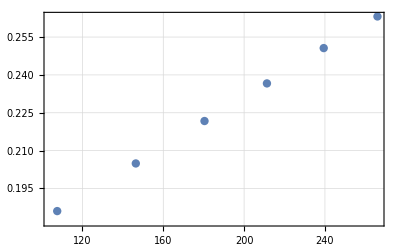

```mathematica
Clear["Global`*"]
SetDirectory["/Users/royalty/Documents/GitHub/Data-Analysis-Plantform-for-University-Physics-Basic-Experiment"]
(*设置工作路径到工作文件夹*)
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)
data2=Import["sampledata2.txt","Table"];(*注意，这里是以"Table"(表格)格式导入二维数据，前面一维数据的导入只需要"List"(列表)*)
ListPlot[data2,PlotTheme->"Detailed",PlotStyle->Directive[PointSize->0.015]]
number=Length[data2];
```

#### 线性回归模型

FittedModel[0.000487716 x+0.133625]

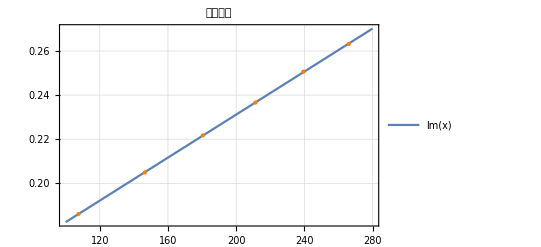

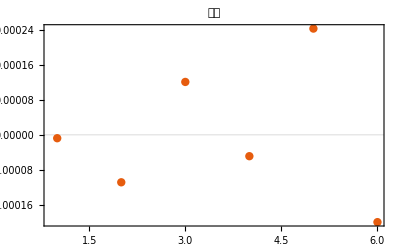

```mathematica
lm=LinearModelFit[data2,x,x];
TraditionalForm[lm]
Show[Plot[lm[x],{x,100,280},PlotLabel->HoldForm[线性回归],PlotTheme->"Detailed"],ListPlot[data2,PlotStyle->Directive[Orange,PointSize->0.015],PlotTheme->"Detailed"]]
ListPlot[lm["FitResiduals"],Frame->True,PlotRange->All,PlotLabel->HoldForm[残差],PlotStyle->Directive[PointSize->0.015],PlotTheme->"Scientific"]
```

#### 不确定度计算

```mathematica
R=-lm["CorrelationMatrix"][[1,2]];
b=lm["BestFitParameters"][[1]];
k=lm["BestFitParameters"][[2]];
Print["相关系数:",R]
Print["截距:",b]
Print["斜率:",k]

Print["各点横坐标:", Table[data2[[i,1]],{i,1,number}]]
Print["横坐标平方平均值：",average=Total[Table[data2[[i,1]]^2,{i,1,number}]]/number]
s1=k*√((1/R-1)/(number-2));
s2=√average*s1;
If[number-2>20,
u2=s2*Tdistribution[[22]];
u1=s1*Tdistribution[[22]],

u2=s2*Tdistribution[[number-2]];
  u1=s1*Tdistribution[[number-2]];
]
Print["斜率标准差:",s1]
Print["截距标准差:",s2]
Print["斜率展伸不确定度:",u1]
Print["截距展伸不确定度:",u2]
```

相关系数:0.962684

截距:0.133625

斜率:0.000487716

各点横坐标:{107.5,146.4,180.4,211.3,239.4,266}

横坐标平方平均值：39708.2

斜率标准差:0.0000480112

截距标准差:0.00956715

斜率展伸不确定度:0.000152676

截距展伸不确定度:0.0304235

### 自定义函数的回归分析

#### 散点图

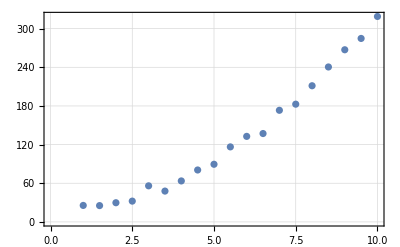

```mathematica
Tdistribution={0,12.71,4.30,3.18,2.78,2.57,2.45,2.36,2.31,2.26,2.23,2.20,2.18,2.16,2.14,2.13,2.12,2.11,2.10,2.09,2.09,1.96};(*这是t分布需要乘的参数列表*)
data=Table[{i,3i^2+20+RandomReal[{-10,10}]},{i,1,10,0.5}];(*这是一些以3x^2+20为中心波
动的随机数列，只是示例*)
ListPlot[data,PlotTheme->"Detailed"]
```

#### 建立回归模型

{x}↦3.02305 x^2-0.167443 x+19.1976

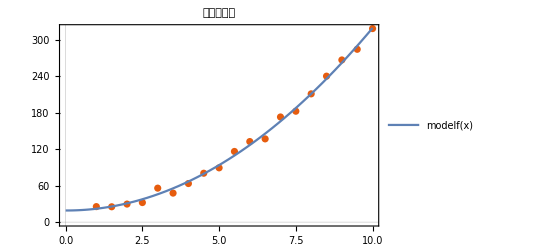

```mathematica
Clear[a,b,c]
model=a x^2+b x+c;
fit=FindFit[data,model,{a,b,c},x];
modelf=Function[{x},Evaluate[model/.fit]];
TraditionalForm[modelf]
Show[ListPlot[data,PlotLabel->HoldForm[非线性回归],PlotTheme->"Scientific"],Plot[modelf[x],{x,0,10},PlotTheme->"Detailed"]]
```

```mathematica
FindFormula[data](*MATHEMATICA内置函数，直接找到一组数据的最佳拟合，可能会与其他方法得到的结果有出入*)
```

17.3506+3.01904 #1^2.&

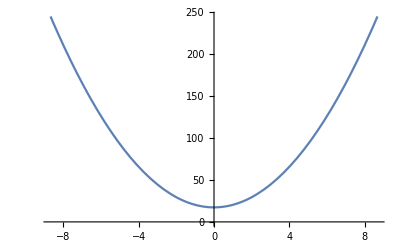

```mathematica
Plot[(17.35059866445689+3.019036910826073 #1^2.&)[x],{x,-8.687687999154425,8.687687999154425}]
```